# 波动方程

## 一维波动方程

振动的吉他弦可以近似地用一维波动方程来描述 :

(∂^2 u)/(∂t^2)=c^2(∂^2 u)/(∂x^2)

这里的 u 表示的是吉他弦偏离平衡位置的距离，t 是时间，x 指琴弦上的点到上弦枕的距离。c 代表弦上的振动波传播的速度，c=√(T/μ)  , 它由弦的张力 T 和单位长度上弦的质量 μ 两个因数共同决定。

首先初始位置条件我们暂时这样表示 :

u(0,x)=0.5 e^(-100(x-1)^2)

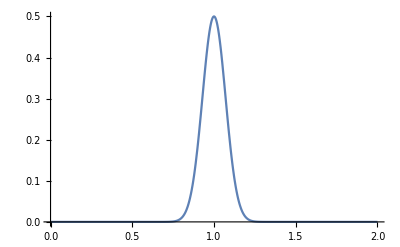

```mathematica
Plot[0.5 E^(-100(x-1)^2),{x,0,2},PlotRange->All]
```

```mathematica
Manipulate[sol=NDSolveValue[{D[u[t,x], {t,2}]==c^2(D[u[t,x], {x,2}]),
u[t,0]==0,u[t,2]==0,u[0,x]==0.5 E^(-100(x-1)^2),
Derivative[1,0][u][0,x]==0},u[t,x],{t,0,20},{x,0,2}];
Plot[sol/.t->tt,{x,0,2},PlotRange->0.5],{{c,0.15},0.1,0.5},{tt,0,20},{sol,ControlType->None}]
```

## 二维波动方程

```mathematica
Plot3D[0.5E^(-100((x-1)^2+(y-1)^2)),{x,0,2},{y,0,2},PlotRange->0.5]
```

-Graphics3D-

### 二维波动微分方程

(∂^2 u)/(∂t^2)=c^2((∂^2 u)/(∂x^2)+(∂^2 u)/(∂x^2))

```mathematica
sol=NDSolveValue[{D[u[t,x,y], t,t]==0.1^2(D[u[t,x,y], x,x]+D[u[t,x,y], y,y]),u[t,0,y]==u[t,2,y]==u[t,x,0]==u[t,x,2]==0,
u[0,x,y]==0.5E^(-100((x-1)^2+(y-1)^2)),
Derivative[1,0,0][u][0,x,y]==0},u[t,x,y],{t,0,10},{x,0,2},{y,0,2}]
```

InterpolatingFunction[…][t,x,y]

```mathematica
ani=ListAnimate[Table[Plot3D[sol/.t->tt,{x,0,2},{y,0,2},PlotRange->0.5,Mesh->None,PlotPoints->30],
{tt,0,10,0.5}]]
```

```mathematica
Export[NotebookDirectory[]<>"wave2D.gif",ani]
```

### 多点波动